```mathematica
ClearAll
```

ClearAll

```mathematica
SetDirectory["G:\\My Drive\\U\\paper"]
```

G:\My Drive\U\paper

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma052+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gamma052=0.52;
gammap002=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points1=Table[{z,omegade[z]},{z,0,1,0.01}]
points5=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.7},{0.01,0.66377},{0.02,0.627756},{0.03,0.592363},{0.04,0.557918},{0.05,0.52468},{0.06,0.492837},{0.07,0.462518},{0.08,0.433799},{0.09,0.406715},{0.1,0.381264},{0.11,0.357419},{0.12,0.335132},{0.13,0.314342},{0.14,0.294978},{0.15,0.276963},{0.16,0.260216},{0.17,0.244658},{0.18,0.230209},{0.19,0.216793},{0.2,0.204334},{0.21,0.192763},{0.22,0.182013},{0.23,0.172023},{0.24,0.162733},{0.25,0.154091},{0.26,0.146047},{0.27,0.138553},{0.28,0.131568},{0.29,0.125051},{0.3,0.118968},{0.31,0.113284},{0.32,0.10797},{0.33,0.102997},{0.34,0.0983395},{0.35,0.0939738},{0.36,0.0898783},{0.37,0.0860332},{0.38,0.0824202},{0.39,0.0790224},{0.4,0.0758245},{0.41,0.0728123},{0.42,0.0699727},{0.43,0.0672937},{0.44,0.0647643},{0.45,0.0623743},{0.46,0.0601143},{0.47,0.0579757},{0.48,0.0559504},{0.49,0.0540309},{0.5,0.0522106},{0.51,0.0504831},{0.52,0.0488425},{0.53,0.0472833},{0.54,0.0458007},{0.55,0.0443898},{0.56,0.0430463},{0.57,0.0417663},{0.58,0.0405459},{0.59,0.0393817},{0.6,0.0382705},{0.61,0.0372092},{0.62,0.036195},{0.63,0.0352252},{0.64,0.0342974},{0.65,0.0334093},{0.66,0.0325587},{0.67,0.0317437},{0.68,0.0309623},{0.69,0.0302129},{0.7,0.0294936},{0.71,0.0288031},{0.72,0.0281397},{0.73,0.0275022},{0.74,0.0268893},{0.75,0.0262997},{0.76,0.0257324},{0.77,0.0251862},{0.78,0.0246601},{0.79,0.0241533},{0.8,0.0236647},{0.81,0.0231935},{0.82,0.022739},{0.83,0.0223003},{0.84,0.0218769},{0.85,0.0214679},{0.86,0.0210728},{0.87,0.0206909},{0.88,0.0203217},{0.89,0.0199646},{0.9,0.0196191},{0.91,0.0192848},{0.92,0.0189611},{0.93,0.0186477},{0.94,0.018344},{0.95,0.0180498},{0.96,0.0177646},{0.97,0.0174881},{0.98,0.0172199},{0.99,0.0169596},{1.,0.0167071}}

{{0.,0.3},{0.01,0.33623},{0.02,0.372244},{0.03,0.407637},{0.04,0.442082},{0.05,0.47532},{0.06,0.507163},{0.07,0.537482},{0.08,0.566201},{0.09,0.593285},{0.1,0.618736},{0.11,0.642581},{0.12,0.664868},{0.13,0.685658},{0.14,0.705022},{0.15,0.723037},{0.16,0.739784},{0.17,0.755342},{0.18,0.769791},{0.19,0.783207},{0.2,0.795666},{0.21,0.807237},{0.22,0.817987},{0.23,0.827977},{0.24,0.837267},{0.25,0.845909},{0.26,0.853953},{0.27,0.861447},{0.28,0.868432},{0.29,0.874949},{0.3,0.881032},{0.31,0.886716},{0.32,0.89203},{0.33,0.897003},{0.34,0.901661},{0.35,0.906026},{0.36,0.910122},{0.37,0.913967},{0.38,0.91758},{0.39,0.920978},{0.4,0.924176},{0.41,0.927188},{0.42,0.930027},{0.43,0.932706},{0.44,0.935236},{0.45,0.937626},{0.46,0.939886},{0.47,0.942024},{0.48,0.94405},{0.49,0.945969},{0.5,0.947789},{0.51,0.949517},{0.52,0.951158},{0.53,0.952717},{0.54,0.954199},{0.55,0.95561},{0.56,0.956954},{0.57,0.958234},{0.58,0.959454},{0.59,0.960618},{0.6,0.961729},{0.61,0.962791},{0.62,0.963805},{0.63,0.964775},{0.64,0.965703},{0.65,0.966591},{0.66,0.967441},{0.67,0.968256},{0.68,0.969038},{0.69,0.969787},{0.7,0.970506},{0.71,0.971197},{0.72,0.97186},{0.73,0.972498},{0.74,0.973111},{0.75,0.9737},{0.76,0.974268},{0.77,0.974814},{0.78,0.97534},{0.79,0.975847},{0.8,0.976335},{0.81,0.976807},{0.82,0.977261},{0.83,0.9777},{0.84,0.978123},{0.85,0.978532},{0.86,0.978927},{0.87,0.979309},{0.88,0.979678},{0.89,0.980035},{0.9,0.980381},{0.91,0.980715},{0.92,0.981039},{0.93,0.981352},{0.94,0.981656},{0.95,0.98195},{0.96,0.982235},{0.97,0.982512},{0.98,0.98278},{0.99,0.98304},{1.,0.983293}}

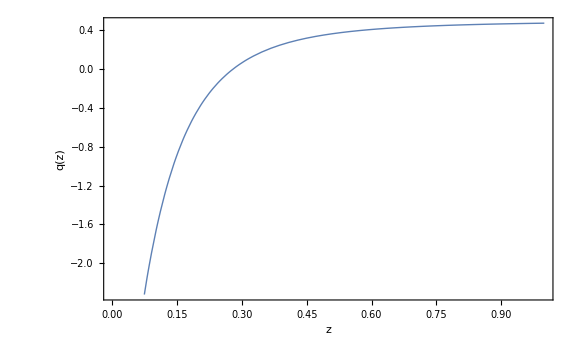

```mathematica
p04n=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma2[a_]=gamma055+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma2[a];
```

```mathematica
gamma055=0.55;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points2=Table[{z,omegade[z]},{z,0,1,0.01}]
points6=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.7},{0.01,0.688584},{0.02,0.677302},{0.03,0.666167},{0.04,0.655191},{0.05,0.644381},{0.06,0.633747},{0.07,0.623295},{0.08,0.61303},{0.09,0.602956},{0.1,0.593078},{0.11,0.583396},{0.12,0.573912},{0.13,0.564629},{0.14,0.555544},{0.15,0.546659},{0.16,0.537972},{0.17,0.529481},{0.18,0.521186},{0.19,0.513082},{0.2,0.505169},{0.21,0.497444},{0.22,0.489902},{0.23,0.482542},{0.24,0.47536},{0.25,0.468353},{0.26,0.461516},{0.27,0.454847},{0.28,0.448342},{0.29,0.441997},{0.3,0.435808},{0.31,0.429772},{0.32,0.423885},{0.33,0.418143},{0.34,0.412544},{0.35,0.407082},{0.36,0.401755},{0.37,0.39656},{0.38,0.391492},{0.39,0.386548},{0.4,0.381726},{0.41,0.377021},{0.42,0.372431},{0.43,0.367953},{0.44,0.363582},{0.45,0.359318},{0.46,0.355156},{0.47,0.351094},{0.48,0.347129},{0.49,0.343258},{0.5,0.339479},{0.51,0.335789},{0.52,0.332186},{0.53,0.328668},{0.54,0.325231},{0.55,0.321874},{0.56,0.318595},{0.57,0.315392},{0.58,0.312262},{0.59,0.309203},{0.6,0.306213},{0.61,0.303292},{0.62,0.300435},{0.63,0.297643},{0.64,0.294913},{0.65,0.292244},{0.66,0.289633},{0.67,0.28708},{0.68,0.284583},{0.69,0.28214},{0.7,0.27975},{0.71,0.277411},{0.72,0.275123},{0.73,0.272883},{0.74,0.270691},{0.75,0.268545},{0.76,0.266445},{0.77,0.264388},{0.78,0.262374},{0.79,0.260402},{0.8,0.25847},{0.81,0.256579},{0.82,0.254726},{0.83,0.25291},{0.84,0.251132},{0.85,0.249389},{0.86,0.247681},{0.87,0.246007},{0.88,0.244367},{0.89,0.242759},{0.9,0.241183},{0.91,0.239637},{0.92,0.238122},{0.93,0.236636},{0.94,0.23518},{0.95,0.233751},{0.96,0.232349},{0.97,0.230974},{0.98,0.229626},{0.99,0.228303},{1.,0.227005}}

{{0.,0.3},{0.01,0.311416},{0.02,0.322698},{0.03,0.333833},{0.04,0.344809},{0.05,0.355619},{0.06,0.366253},{0.07,0.376705},{0.08,0.38697},{0.09,0.397044},{0.1,0.406922},{0.11,0.416604},{0.12,0.426088},{0.13,0.435371},{0.14,0.444456},{0.15,0.453341},{0.16,0.462028},{0.17,0.470519},{0.18,0.478814},{0.19,0.486918},{0.2,0.494831},{0.21,0.502556},{0.22,0.510098},{0.23,0.517458},{0.24,0.52464},{0.25,0.531647},{0.26,0.538484},{0.27,0.545153},{0.28,0.551658},{0.29,0.558003},{0.3,0.564192},{0.31,0.570228},{0.32,0.576115},{0.33,0.581857},{0.34,0.587456},{0.35,0.592918},{0.36,0.598245},{0.37,0.60344},{0.38,0.608508},{0.39,0.613452},{0.4,0.618274},{0.41,0.622979},{0.42,0.627569},{0.43,0.632047},{0.44,0.636418},{0.45,0.640682},{0.46,0.644844},{0.47,0.648906},{0.48,0.652871},{0.49,0.656742},{0.5,0.660521},{0.51,0.664211},{0.52,0.667814},{0.53,0.671332},{0.54,0.674769},{0.55,0.678126},{0.56,0.681405},{0.57,0.684608},{0.58,0.687738},{0.59,0.690797},{0.6,0.693787},{0.61,0.696708},{0.62,0.699565},{0.63,0.702357},{0.64,0.705087},{0.65,0.707756},{0.66,0.710367},{0.67,0.71292},{0.68,0.715417},{0.69,0.71786},{0.7,0.72025},{0.71,0.722589},{0.72,0.724877},{0.73,0.727117},{0.74,0.729309},{0.75,0.731455},{0.76,0.733555},{0.77,0.735612},{0.78,0.737626},{0.79,0.739598},{0.8,0.74153},{0.81,0.743421},{0.82,0.745274},{0.83,0.74709},{0.84,0.748868},{0.85,0.750611},{0.86,0.752319},{0.87,0.753993},{0.88,0.755633},{0.89,0.757241},{0.9,0.758817},{0.91,0.760363},{0.92,0.761878},{0.93,0.763364},{0.94,0.76482},{0.95,0.766249},{0.96,0.767651},{0.97,0.769026},{0.98,0.770374},{0.99,0.771697},{1.,0.772995}}

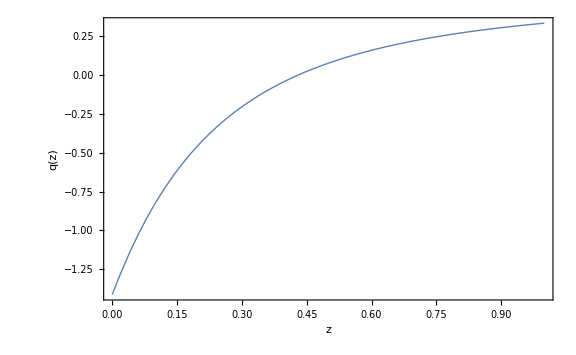

```mathematica
p02n=Plot[q[z],{z,0,1},PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma3[a_]=gamma059+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma3[a];
```

```mathematica
gamma059=0.59;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points3=Table[{z,omegade[z]},{z,0,1,0.01}]
points7=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.7},{0.01,0.695899},{0.02,0.691865},{0.03,0.687896},{0.04,0.683992},{0.05,0.680153},{0.06,0.676377},{0.07,0.672664},{0.08,0.669012},{0.09,0.665422},{0.1,0.661893},{0.11,0.658422},{0.12,0.655011},{0.13,0.651657},{0.14,0.64836},{0.15,0.645119},{0.16,0.641933},{0.17,0.638801},{0.18,0.635723},{0.19,0.632698},{0.2,0.629724},{0.21,0.6268},{0.22,0.623927},{0.23,0.621103},{0.24,0.618327},{0.25,0.615598},{0.26,0.612916},{0.27,0.61028},{0.28,0.607688},{0.29,0.605141},{0.3,0.602637},{0.31,0.600176},{0.32,0.597757},{0.33,0.595378},{0.34,0.59304},{0.35,0.590742},{0.36,0.588482},{0.37,0.586261},{0.38,0.584077},{0.39,0.581929},{0.4,0.579818},{0.41,0.577743},{0.42,0.575702},{0.43,0.573696},{0.44,0.571723},{0.45,0.569783},{0.46,0.567875},{0.47,0.565999},{0.48,0.564154},{0.49,0.56234},{0.5,0.560556},{0.51,0.558802},{0.52,0.557076},{0.53,0.55538},{0.54,0.55371},{0.55,0.552069},{0.56,0.550454},{0.57,0.548866},{0.58,0.547304},{0.59,0.545767},{0.6,0.544256},{0.61,0.542769},{0.62,0.541306},{0.63,0.539867},{0.64,0.538452},{0.65,0.537059},{0.66,0.535689},{0.67,0.534341},{0.68,0.533015},{0.69,0.53171},{0.7,0.530427},{0.71,0.529164},{0.72,0.527921},{0.73,0.526698},{0.74,0.525495},{0.75,0.524311},{0.76,0.523145},{0.77,0.521999},{0.78,0.520871},{0.79,0.519761},{0.8,0.518668},{0.81,0.517593},{0.82,0.516535},{0.83,0.515494},{0.84,0.514469},{0.85,0.513461},{0.86,0.512468},{0.87,0.511491},{0.88,0.51053},{0.89,0.509584},{0.9,0.508653},{0.91,0.507736},{0.92,0.506835},{0.93,0.505947},{0.94,0.505073},{0.95,0.504213},{0.96,0.503367},{0.97,0.502534},{0.98,0.501714},{0.99,0.500907},{1.,0.500113}}

{{0.,0.3},{0.01,0.304101},{0.02,0.308135},{0.03,0.312104},{0.04,0.316008},{0.05,0.319847},{0.06,0.323623},{0.07,0.327336},{0.08,0.330988},{0.09,0.334578},{0.1,0.338107},{0.11,0.341578},{0.12,0.344989},{0.13,0.348343},{0.14,0.35164},{0.15,0.354881},{0.16,0.358067},{0.17,0.361199},{0.18,0.364277},{0.19,0.367302},{0.2,0.370276},{0.21,0.3732},{0.22,0.376073},{0.23,0.378897},{0.24,0.381673},{0.25,0.384402},{0.26,0.387084},{0.27,0.38972},{0.28,0.392312},{0.29,0.394859},{0.3,0.397363},{0.31,0.399824},{0.32,0.402243},{0.33,0.404622},{0.34,0.40696},{0.35,0.409258},{0.36,0.411518},{0.37,0.413739},{0.38,0.415923},{0.39,0.418071},{0.4,0.420182},{0.41,0.422257},{0.42,0.424298},{0.43,0.426304},{0.44,0.428277},{0.45,0.430217},{0.46,0.432125},{0.47,0.434001},{0.48,0.435846},{0.49,0.43766},{0.5,0.439444},{0.51,0.441198},{0.52,0.442924},{0.53,0.44462},{0.54,0.44629},{0.55,0.447931},{0.56,0.449546},{0.57,0.451134},{0.58,0.452696},{0.59,0.454233},{0.6,0.455744},{0.61,0.457231},{0.62,0.458694},{0.63,0.460133},{0.64,0.461548},{0.65,0.462941},{0.66,0.464311},{0.67,0.465659},{0.68,0.466985},{0.69,0.46829},{0.7,0.469573},{0.71,0.470836},{0.72,0.472079},{0.73,0.473302},{0.74,0.474505},{0.75,0.475689},{0.76,0.476855},{0.77,0.478001},{0.78,0.479129},{0.79,0.480239},{0.8,0.481332},{0.81,0.482407},{0.82,0.483465},{0.83,0.484506},{0.84,0.485531},{0.85,0.486539},{0.86,0.487532},{0.87,0.488509},{0.88,0.48947},{0.89,0.490416},{0.9,0.491347},{0.91,0.492264},{0.92,0.493165},{0.93,0.494053},{0.94,0.494927},{0.95,0.495787},{0.96,0.496633},{0.97,0.497466},{0.98,0.498286},{0.99,0.499093},{1.,0.499887}}

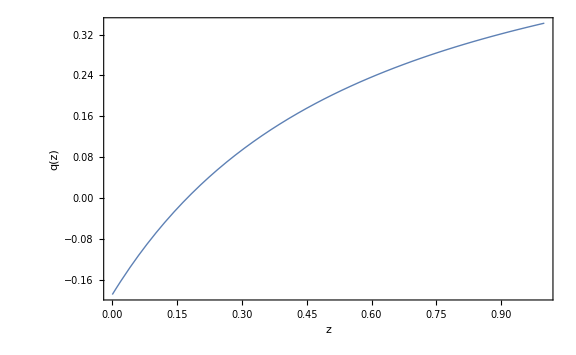

```mathematica
p02=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

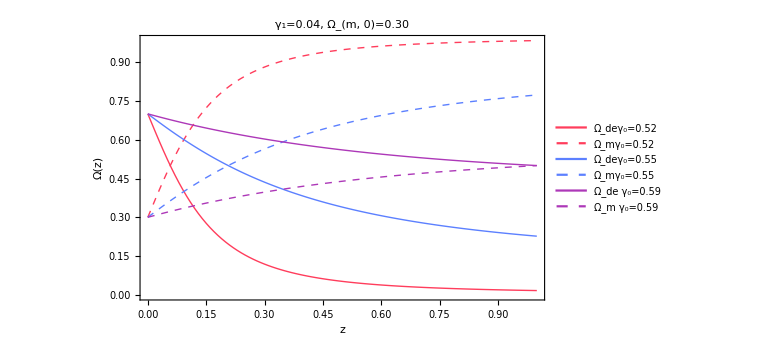

```mathematica
list2=ListLinePlot[{points1,points5,points2, points6, points3, points7}, PlotStyle->{{Thick, RGBColor[1,0.24,0.36]}, {Thick,Dashed, RGBColor[1,0.24,0.36]},{Thick, RGBColor[0.36,0.5,1]}, {Thick,Dashed, RGBColor[0.36,0.5,1]},{Thick, RGBColor[0.68,0.22,0.72]}, {Thick,Dashed, RGBColor[0.68,0.22,0.72]},{Thick, RGBColor[0.31,0.82,0]}, {Thick, Dashed,RGBColor[0.31,0.82,0]}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24,  FontFamily->"Helvetica"],Style["Ω(z)", Black, FontSize->24,  FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"Ω_deγ_0=0.52","Ω_mγ_0=0.52", "Ω_deγ_0=0.55","Ω_mγ_0=0.55", "Ω_de γ_0=0.59", "Ω_m γ_0=0.59","Ω_deγ_1=0.04", "Ω_mγ_1=0.04"}, Background->White, LabelStyle->{FontSize->7}, LegendMarkerSize->{{20,10}}],{Right, Center}], PlotLabel->Style["γ_1=0.04, Ω_(m, 0)=0.30", Black, FontSize->20,  FontFamily->"Helvetica"], Axes->False]
```

```mathematica
Export["omega(z)_gamma1_0.04_om0.30.pdf",list2,ImageResolution->500]
```

omega(z)_gamma1_0.04_om0.30.pdf

```mathematica
ClearAll
```

ClearAll

```mathematica
SetDirectory["G:\\My Drive\\U\\paper"]
```

G:\My Drive\U\paper

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma052+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.28;
gamma052=0.52;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points1=Table[{z,omegade[z]},{z,0,1,0.01}]
points5=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.72},{0.01,0.685099},{0.02,0.650166},{0.03,0.615598},{0.04,0.58173},{0.05,0.548835},{0.06,0.517121},{0.07,0.486741},{0.08,0.4578},{0.09,0.430356},{0.1,0.404434},{0.11,0.38003},{0.12,0.357117},{0.13,0.335652},{0.14,0.315579},{0.15,0.296835},{0.16,0.279351},{0.17,0.263056},{0.18,0.247877},{0.19,0.233743},{0.2,0.220585},{0.21,0.208334},{0.22,0.196928},{0.23,0.186306},{0.24,0.176409},{0.25,0.167186},{0.26,0.158586},{0.27,0.150562},{0.28,0.143072},{0.29,0.136075},{0.3,0.129535},{0.31,0.123417},{0.32,0.117691},{0.33,0.112326},{0.34,0.107297},{0.35,0.102579},{0.36,0.0981495},{0.37,0.093987},{0.38,0.0900729},{0.39,0.0863893},{0.4,0.0829201},{0.41,0.0796503},{0.42,0.0765661},{0.43,0.0736546},{0.44,0.0709044},{0.45,0.0683043},{0.46,0.0658446},{0.47,0.0635158},{0.48,0.0613095},{0.49,0.0592178},{0.5,0.0572333},{0.51,0.0553493},{0.52,0.0535595},{0.53,0.0518579},{0.54,0.0502394},{0.55,0.0486987},{0.56,0.0472313},{0.57,0.0458328},{0.58,0.0444992},{0.59,0.0432266},{0.6,0.0420116},{0.61,0.0408509},{0.62,0.0397415},{0.63,0.0386805},{0.64,0.0376653},{0.65,0.0366933},{0.66,0.0357623},{0.67,0.0348699},{0.68,0.0340143},{0.69,0.0331935},{0.7,0.0324057},{0.71,0.0316491},{0.72,0.0309224},{0.73,0.0302238},{0.74,0.029552},{0.75,0.0289058},{0.76,0.0282839},{0.77,0.0276851},{0.78,0.0271083},{0.79,0.0265524},{0.8,0.0260166},{0.81,0.0254998},{0.82,0.0250013},{0.83,0.0245201},{0.84,0.0240555},{0.85,0.0236068},{0.86,0.0231732},{0.87,0.0227542},{0.88,0.022349},{0.89,0.0219571},{0.9,0.0215779},{0.91,0.0212109},{0.92,0.0208556},{0.93,0.0205115},{0.94,0.0201781},{0.95,0.019855},{0.96,0.0195419},{0.97,0.0192382},{0.98,0.0189437},{0.99,0.0186579},{1.,0.0183806}}

{{0.,0.28},{0.01,0.314901},{0.02,0.349834},{0.03,0.384402},{0.04,0.41827},{0.05,0.451165},{0.06,0.482879},{0.07,0.513259},{0.08,0.5422},{0.09,0.569644},{0.1,0.595566},{0.11,0.61997},{0.12,0.642883},{0.13,0.664348},{0.14,0.684421},{0.15,0.703165},{0.16,0.720649},{0.17,0.736944},{0.18,0.752123},{0.19,0.766257},{0.2,0.779415},{0.21,0.791666},{0.22,0.803072},{0.23,0.813694},{0.24,0.823591},{0.25,0.832814},{0.26,0.841414},{0.27,0.849438},{0.28,0.856928},{0.29,0.863925},{0.3,0.870465},{0.31,0.876583},{0.32,0.882309},{0.33,0.887674},{0.34,0.892703},{0.35,0.897421},{0.36,0.901851},{0.37,0.906013},{0.38,0.909927},{0.39,0.913611},{0.4,0.91708},{0.41,0.92035},{0.42,0.923434},{0.43,0.926345},{0.44,0.929096},{0.45,0.931696},{0.46,0.934155},{0.47,0.936484},{0.48,0.93869},{0.49,0.940782},{0.5,0.942767},{0.51,0.944651},{0.52,0.946441},{0.53,0.948142},{0.54,0.949761},{0.55,0.951301},{0.56,0.952769},{0.57,0.954167},{0.58,0.955501},{0.59,0.956773},{0.6,0.957988},{0.61,0.959149},{0.62,0.960258},{0.63,0.961319},{0.64,0.962335},{0.65,0.963307},{0.66,0.964238},{0.67,0.96513},{0.68,0.965986},{0.69,0.966807},{0.7,0.967594},{0.71,0.968351},{0.72,0.969078},{0.73,0.969776},{0.74,0.970448},{0.75,0.971094},{0.76,0.971716},{0.77,0.972315},{0.78,0.972892},{0.79,0.973448},{0.8,0.973983},{0.81,0.9745},{0.82,0.974999},{0.83,0.97548},{0.84,0.975944},{0.85,0.976393},{0.86,0.976827},{0.87,0.977246},{0.88,0.977651},{0.89,0.978043},{0.9,0.978422},{0.91,0.978789},{0.92,0.979144},{0.93,0.979489},{0.94,0.979822},{0.95,0.980145},{0.96,0.980458},{0.97,0.980762},{0.98,0.981056},{0.99,0.981342},{1.,0.981619}}

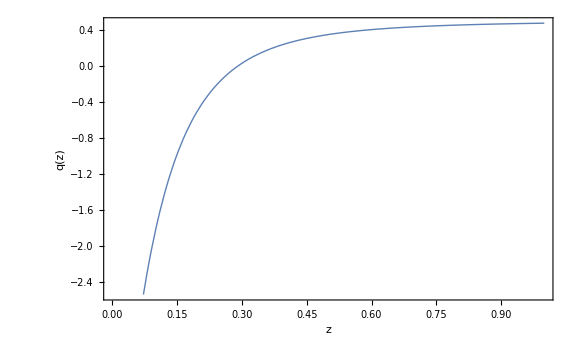

```mathematica
p04n=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma2[a_]=gamma055+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma2[a];
```

```mathematica
gamma055=0.55;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points2=Table[{z,omegade[z]},{z,0,1,0.01}]
points6=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.72},{0.01,0.708761},{0.02,0.697629},{0.03,0.686618},{0.04,0.675739},{0.05,0.665004},{0.06,0.654423},{0.07,0.644002},{0.08,0.63375},{0.09,0.623672},{0.1,0.613772},{0.11,0.604055},{0.12,0.594522},{0.13,0.585176},{0.14,0.576018},{0.15,0.567049},{0.16,0.558269},{0.17,0.549677},{0.18,0.541272},{0.19,0.533053},{0.2,0.525018},{0.21,0.517165},{0.22,0.509492},{0.23,0.501996},{0.24,0.494674},{0.25,0.487524},{0.26,0.480543},{0.27,0.473727},{0.28,0.467073},{0.29,0.460578},{0.3,0.454239},{0.31,0.448051},{0.32,0.442013},{0.33,0.436119},{0.34,0.430368},{0.35,0.424755},{0.36,0.419277},{0.37,0.413931},{0.38,0.408714},{0.39,0.403622},{0.4,0.398652},{0.41,0.393801},{0.42,0.389066},{0.43,0.384444},{0.44,0.379932},{0.45,0.375527},{0.46,0.371226},{0.47,0.367026},{0.48,0.362925},{0.49,0.358921},{0.5,0.35501},{0.51,0.351189},{0.52,0.347458},{0.53,0.343812},{0.54,0.340251},{0.55,0.336771},{0.56,0.33337},{0.57,0.330047},{0.58,0.326799},{0.59,0.323624},{0.6,0.32052},{0.61,0.317486},{0.62,0.314519},{0.63,0.311617},{0.64,0.30878},{0.65,0.306005},{0.66,0.303291},{0.67,0.300635},{0.68,0.298037},{0.69,0.295495},{0.7,0.293008},{0.71,0.290573},{0.72,0.288191},{0.73,0.285858},{0.74,0.283575},{0.75,0.28134},{0.76,0.279151},{0.77,0.277008},{0.78,0.274909},{0.79,0.272853},{0.8,0.270839},{0.81,0.268866},{0.82,0.266933},{0.83,0.26504},{0.84,0.263184},{0.85,0.261365},{0.86,0.259583},{0.87,0.257836},{0.88,0.256123},{0.89,0.254444},{0.9,0.252798},{0.91,0.251184},{0.92,0.249602},{0.93,0.24805},{0.94,0.246527},{0.95,0.245034},{0.96,0.24357},{0.97,0.242133},{0.98,0.240723},{0.99,0.23934},{1.,0.237983}}

{{0.,0.28},{0.01,0.291239},{0.02,0.302371},{0.03,0.313382},{0.04,0.324261},{0.05,0.334996},{0.06,0.345577},{0.07,0.355998},{0.08,0.36625},{0.09,0.376328},{0.1,0.386228},{0.11,0.395945},{0.12,0.405478},{0.13,0.414824},{0.14,0.423982},{0.15,0.432951},{0.16,0.441731},{0.17,0.450323},{0.18,0.458728},{0.19,0.466947},{0.2,0.474982},{0.21,0.482835},{0.22,0.490508},{0.23,0.498004},{0.24,0.505326},{0.25,0.512476},{0.26,0.519457},{0.27,0.526273},{0.28,0.532927},{0.29,0.539422},{0.3,0.545761},{0.31,0.551949},{0.32,0.557987},{0.33,0.563881},{0.34,0.569632},{0.35,0.575245},{0.36,0.580723},{0.37,0.586069},{0.38,0.591286},{0.39,0.596378},{0.4,0.601348},{0.41,0.606199},{0.42,0.610934},{0.43,0.615556},{0.44,0.620068},{0.45,0.624473},{0.46,0.628774},{0.47,0.632974},{0.48,0.637075},{0.49,0.641079},{0.5,0.64499},{0.51,0.648811},{0.52,0.652542},{0.53,0.656188},{0.54,0.659749},{0.55,0.663229},{0.56,0.66663},{0.57,0.669953},{0.58,0.673201},{0.59,0.676376},{0.6,0.67948},{0.61,0.682514},{0.62,0.685481},{0.63,0.688383},{0.64,0.69122},{0.65,0.693995},{0.66,0.696709},{0.67,0.699365},{0.68,0.701963},{0.69,0.704505},{0.7,0.706992},{0.71,0.709427},{0.72,0.711809},{0.73,0.714142},{0.74,0.716425},{0.75,0.71866},{0.76,0.720849},{0.77,0.722992},{0.78,0.725091},{0.79,0.727147},{0.8,0.729161},{0.81,0.731134},{0.82,0.733067},{0.83,0.73496},{0.84,0.736816},{0.85,0.738635},{0.86,0.740417},{0.87,0.742164},{0.88,0.743877},{0.89,0.745556},{0.9,0.747202},{0.91,0.748816},{0.92,0.750398},{0.93,0.75195},{0.94,0.753473},{0.95,0.754966},{0.96,0.75643},{0.97,0.757867},{0.98,0.759277},{0.99,0.76066},{1.,0.762017}}

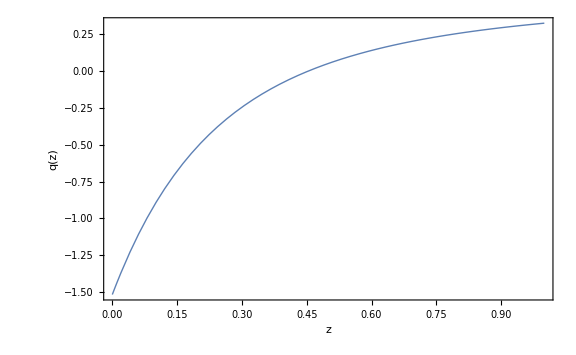

```mathematica
p02n=Plot[q[z],{z,0,1},PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma3[a_]=gamma059+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma3[a];
```

```mathematica
gamma059=0.59;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points3=Table[{z,omegade[z]},{z,0,1,0.01}]
points7=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.72},{0.01,0.715902},{0.02,0.711867},{0.03,0.707893},{0.04,0.703981},{0.05,0.700129},{0.06,0.696338},{0.07,0.692607},{0.08,0.688935},{0.09,0.685321},{0.1,0.681765},{0.11,0.678266},{0.12,0.674824},{0.13,0.671438},{0.14,0.668107},{0.15,0.664829},{0.16,0.661606},{0.17,0.658435},{0.18,0.655316},{0.19,0.652249},{0.2,0.649232},{0.21,0.646264},{0.22,0.643346},{0.23,0.640476},{0.24,0.637653},{0.25,0.634876},{0.26,0.632146},{0.27,0.629461},{0.28,0.62682},{0.29,0.624222},{0.3,0.621668},{0.31,0.619156},{0.32,0.616685},{0.33,0.614255},{0.34,0.611865},{0.35,0.609515},{0.36,0.607203},{0.37,0.604929},{0.38,0.602693},{0.39,0.600493},{0.4,0.598329},{0.41,0.596201},{0.42,0.594108},{0.43,0.592048},{0.44,0.590023},{0.45,0.58803},{0.46,0.58607},{0.47,0.584142},{0.48,0.582245},{0.49,0.580379},{0.5,0.578543},{0.51,0.576737},{0.52,0.57496},{0.53,0.573212},{0.54,0.571492},{0.55,0.569799},{0.56,0.568134},{0.57,0.566496},{0.58,0.564883},{0.59,0.563297},{0.6,0.561736},{0.61,0.5602},{0.62,0.558688},{0.63,0.5572},{0.64,0.555736},{0.65,0.554295},{0.66,0.552878},{0.67,0.551482},{0.68,0.550109},{0.69,0.548757},{0.7,0.547427},{0.71,0.546117},{0.72,0.544828},{0.73,0.54356},{0.74,0.542311},{0.75,0.541082},{0.76,0.539872},{0.77,0.538681},{0.78,0.537509},{0.79,0.536355},{0.8,0.535219},{0.81,0.534101},{0.82,0.533},{0.83,0.531916},{0.84,0.530849},{0.85,0.529799},{0.86,0.528765},{0.87,0.527747},{0.88,0.526744},{0.89,0.525758},{0.9,0.524786},{0.91,0.52383},{0.92,0.522888},{0.93,0.521961},{0.94,0.521049},{0.95,0.52015},{0.96,0.519265},{0.97,0.518394},{0.98,0.517537},{0.99,0.516692},{1.,0.515861}}

{{0.,0.28},{0.01,0.284098},{0.02,0.288133},{0.03,0.292107},{0.04,0.296019},{0.05,0.299871},{0.06,0.303662},{0.07,0.307393},{0.08,0.311065},{0.09,0.314679},{0.1,0.318235},{0.11,0.321734},{0.12,0.325176},{0.13,0.328562},{0.14,0.331893},{0.15,0.335171},{0.16,0.338394},{0.17,0.341565},{0.18,0.344684},{0.19,0.347751},{0.2,0.350768},{0.21,0.353736},{0.22,0.356654},{0.23,0.359524},{0.24,0.362347},{0.25,0.365124},{0.26,0.367854},{0.27,0.370539},{0.28,0.37318},{0.29,0.375778},{0.3,0.378332},{0.31,0.380844},{0.32,0.383315},{0.33,0.385745},{0.34,0.388135},{0.35,0.390485},{0.36,0.392797},{0.37,0.395071},{0.38,0.397307},{0.39,0.399507},{0.4,0.401671},{0.41,0.403799},{0.42,0.405892},{0.43,0.407952},{0.44,0.409977},{0.45,0.41197},{0.46,0.41393},{0.47,0.415858},{0.48,0.417755},{0.49,0.419621},{0.5,0.421457},{0.51,0.423263},{0.52,0.42504},{0.53,0.426788},{0.54,0.428508},{0.55,0.430201},{0.56,0.431866},{0.57,0.433504},{0.58,0.435117},{0.59,0.436703},{0.6,0.438264},{0.61,0.4398},{0.62,0.441312},{0.63,0.4428},{0.64,0.444264},{0.65,0.445705},{0.66,0.447122},{0.67,0.448518},{0.68,0.449891},{0.69,0.451243},{0.7,0.452573},{0.71,0.453883},{0.72,0.455172},{0.73,0.45644},{0.74,0.457689},{0.75,0.458918},{0.76,0.460128},{0.77,0.461319},{0.78,0.462491},{0.79,0.463645},{0.8,0.464781},{0.81,0.465899},{0.82,0.467},{0.83,0.468084},{0.84,0.469151},{0.85,0.470201},{0.86,0.471235},{0.87,0.472253},{0.88,0.473256},{0.89,0.474242},{0.9,0.475214},{0.91,0.47617},{0.92,0.477112},{0.93,0.478039},{0.94,0.478951},{0.95,0.47985},{0.96,0.480735},{0.97,0.481606},{0.98,0.482463},{0.99,0.483308},{1.,0.484139}}

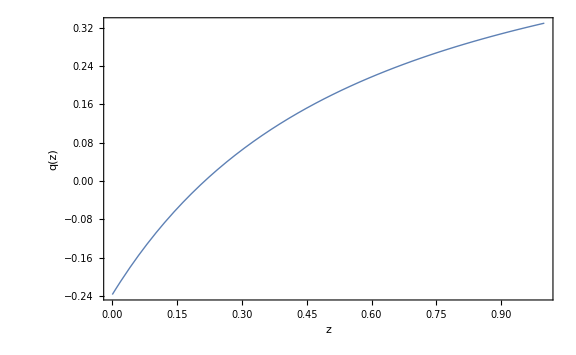

```mathematica
p02=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

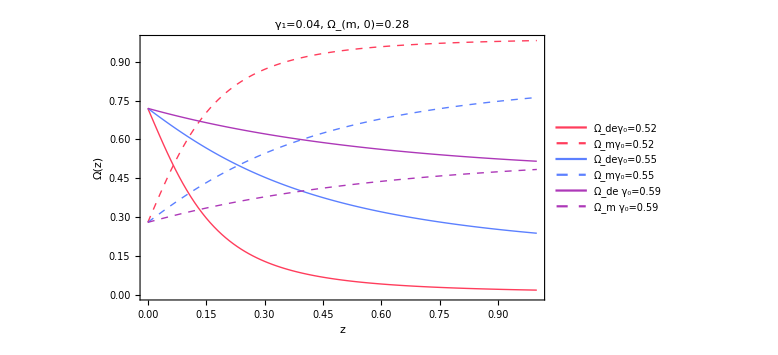

```mathematica
list2=ListLinePlot[{points1,points5,points2, points6, points3, points7}, PlotStyle->{{Thick, RGBColor[1,0.24,0.36]}, {Thick,Dashed, RGBColor[1,0.24,0.36]},{Thick, RGBColor[0.36,0.5,1]}, {Thick,Dashed, RGBColor[0.36,0.5,1]},{Thick, RGBColor[0.68,0.22,0.72]}, {Thick,Dashed, RGBColor[0.68,0.22,0.72]},{Thick, RGBColor[0.31,0.82,0]}, {Thick, Dashed,RGBColor[0.31,0.82,0]}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24,  FontFamily->"Helvetica"],Style["Ω(z)", Black, FontSize->24,  FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"Ω_deγ_0=0.52","Ω_mγ_0=0.52", "Ω_deγ_0=0.55","Ω_mγ_0=0.55", "Ω_de γ_0=0.59", "Ω_m γ_0=0.59","Ω_deγ_1=0.04", "Ω_mγ_1=0.04"}, Background->White, LabelStyle->{FontSize->7}, LegendMarkerSize->{{20,10}}],{Right, Center}], PlotLabel->Style["γ_1=0.04, Ω_(m, 0)=0.28", Black, FontSize->20,  FontFamily->"Helvetica"], Axes->False]
```

```mathematica
Export["omega(z)_gamma1_0.04_om0.28.pdf",list2,ImageResolution->500]
```

omega(z)_gamma1_0.04_om0.28.pdf

```mathematica
ClearAll
```

ClearAll

```mathematica
SetDirectory["G:\\My Drive\\U\\paper"]
```

G:\My Drive\U\paper

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma052+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.32;
gamma052=0.52;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points1=Table[{z,omegade[z]},{z,0,1,0.01}]
points5=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.68},{0.01,0.641917},{0.02,0.60433},{0.03,0.567666},{0.04,0.532259},{0.05,0.498355},{0.06,0.466123},{0.07,0.435664},{0.08,0.407023},{0.09,0.3802},{0.1,0.355163},{0.11,0.331856},{0.12,0.310202},{0.13,0.290118},{0.14,0.271511},{0.15,0.254286},{0.16,0.238349},{0.17,0.223607},{0.18,0.209973},{0.19,0.19736},{0.2,0.18569},{0.21,0.174887},{0.22,0.164882},{0.23,0.15561},{0.24,0.147012},{0.25,0.139033},{0.26,0.131623},{0.27,0.124735},{0.28,0.118328},{0.29,0.112362},{0.3,0.106802},{0.31,0.101617},{0.32,0.0967755},{0.33,0.0922518},{0.34,0.0880208},{0.35,0.0840601},{0.36,0.0803489},{0.37,0.0768686},{0.38,0.0736018},{0.39,0.0705327},{0.4,0.0676469},{0.41,0.0649311},{0.42,0.062373},{0.43,0.0599615},{0.44,0.0576864},{0.45,0.0555382},{0.46,0.0535082},{0.47,0.0515883},{0.48,0.0497713},{0.49,0.0480503},{0.5,0.0464191},{0.51,0.0448718},{0.52,0.043403},{0.53,0.0420078},{0.54,0.0406817},{0.55,0.0394202},{0.56,0.0382196},{0.57,0.0370761},{0.58,0.0359862},{0.59,0.0349469},{0.6,0.0339552},{0.61,0.0330083},{0.62,0.0321038},{0.63,0.0312391},{0.64,0.0304121},{0.65,0.0296206},{0.66,0.0288629},{0.67,0.0281369},{0.68,0.0274411},{0.69,0.0267739},{0.7,0.0261337},{0.71,0.0255191},{0.72,0.0249289},{0.73,0.0243618},{0.74,0.0238167},{0.75,0.0232924},{0.76,0.022788},{0.77,0.0223025},{0.78,0.0218349},{0.79,0.0213844},{0.8,0.0209503},{0.81,0.0205317},{0.82,0.0201279},{0.83,0.0197383},{0.84,0.0193623},{0.85,0.0189991},{0.86,0.0186483},{0.87,0.0183093},{0.88,0.0179815},{0.89,0.0176646},{0.9,0.017358},{0.91,0.0170614},{0.92,0.0167742},{0.93,0.0164961},{0.94,0.0162267},{0.95,0.0159657},{0.96,0.0157127},{0.97,0.0154675},{0.98,0.0152296},{0.99,0.0149989},{1.,0.014775}}

{{0.,0.32},{0.01,0.358083},{0.02,0.39567},{0.03,0.432334},{0.04,0.467741},{0.05,0.501645},{0.06,0.533877},{0.07,0.564336},{0.08,0.592977},{0.09,0.6198},{0.1,0.644837},{0.11,0.668144},{0.12,0.689798},{0.13,0.709882},{0.14,0.728489},{0.15,0.745714},{0.16,0.761651},{0.17,0.776393},{0.18,0.790027},{0.19,0.80264},{0.2,0.81431},{0.21,0.825113},{0.22,0.835118},{0.23,0.84439},{0.24,0.852988},{0.25,0.860967},{0.26,0.868377},{0.27,0.875265},{0.28,0.881672},{0.29,0.887638},{0.3,0.893198},{0.31,0.898383},{0.32,0.903225},{0.33,0.907748},{0.34,0.911979},{0.35,0.91594},{0.36,0.919651},{0.37,0.923131},{0.38,0.926398},{0.39,0.929467},{0.4,0.932353},{0.41,0.935069},{0.42,0.937627},{0.43,0.940038},{0.44,0.942314},{0.45,0.944462},{0.46,0.946492},{0.47,0.948412},{0.48,0.950229},{0.49,0.95195},{0.5,0.953581},{0.51,0.955128},{0.52,0.956597},{0.53,0.957992},{0.54,0.959318},{0.55,0.96058},{0.56,0.96178},{0.57,0.962924},{0.58,0.964014},{0.59,0.965053},{0.6,0.966045},{0.61,0.966992},{0.62,0.967896},{0.63,0.968761},{0.64,0.969588},{0.65,0.970379},{0.66,0.971137},{0.67,0.971863},{0.68,0.972559},{0.69,0.973226},{0.7,0.973866},{0.71,0.974481},{0.72,0.975071},{0.73,0.975638},{0.74,0.976183},{0.75,0.976708},{0.76,0.977212},{0.77,0.977698},{0.78,0.978165},{0.79,0.978616},{0.8,0.97905},{0.81,0.979468},{0.82,0.979872},{0.83,0.980262},{0.84,0.980638},{0.85,0.981001},{0.86,0.981352},{0.87,0.981691},{0.88,0.982018},{0.89,0.982335},{0.9,0.982642},{0.91,0.982939},{0.92,0.983226},{0.93,0.983504},{0.94,0.983773},{0.95,0.984034},{0.96,0.984287},{0.97,0.984533},{0.98,0.98477},{0.99,0.985001},{1.,0.985225}}

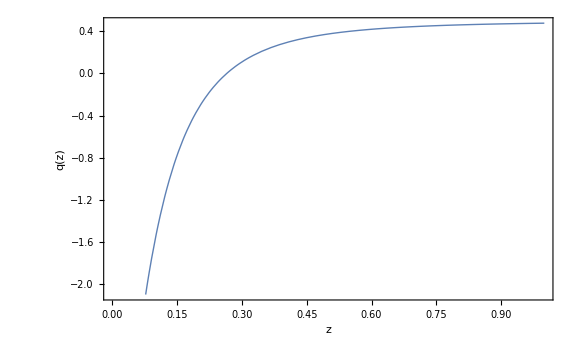

```mathematica
p04n=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma2[a_]=gamma055+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma2[a];
```

```mathematica
gamma055=0.55;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points2=Table[{z,omegade[z]},{z,0,1,0.01}]
points6=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.68},{0.01,0.66845},{0.02,0.657062},{0.03,0.645846},{0.04,0.634811},{0.05,0.623966},{0.06,0.613316},{0.07,0.602866},{0.08,0.592621},{0.09,0.582584},{0.1,0.572755},{0.11,0.563137},{0.12,0.553729},{0.13,0.544532},{0.14,0.535544},{0.15,0.526764},{0.16,0.51819},{0.17,0.509819},{0.18,0.50165},{0.19,0.493678},{0.2,0.485902},{0.21,0.478317},{0.22,0.47092},{0.23,0.463707},{0.24,0.456675},{0.25,0.449819},{0.26,0.443136},{0.27,0.436621},{0.28,0.430271},{0.29,0.424082},{0.3,0.418049},{0.31,0.41217},{0.32,0.406439},{0.33,0.400853},{0.34,0.395408},{0.35,0.390101},{0.36,0.384927},{0.37,0.379883},{0.38,0.374966},{0.39,0.370172},{0.4,0.365498},{0.41,0.360939},{0.42,0.356494},{0.43,0.352159},{0.44,0.34793},{0.45,0.343806},{0.46,0.339782},{0.47,0.335856},{0.48,0.332025},{0.49,0.328286},{0.5,0.324638},{0.51,0.321077},{0.52,0.317601},{0.53,0.314207},{0.54,0.310893},{0.55,0.307658},{0.56,0.304498},{0.57,0.301411},{0.58,0.298397},{0.59,0.295451},{0.6,0.292573},{0.61,0.289762},{0.62,0.287014},{0.63,0.284328},{0.64,0.281702},{0.65,0.279136},{0.66,0.276626},{0.67,0.274172},{0.68,0.271773},{0.69,0.269426},{0.7,0.26713},{0.71,0.264884},{0.72,0.262687},{0.73,0.260537},{0.74,0.258433},{0.75,0.256373},{0.76,0.254358},{0.77,0.252385},{0.78,0.250453},{0.79,0.248562},{0.8,0.24671},{0.81,0.244897},{0.82,0.24312},{0.83,0.241381},{0.84,0.239676},{0.85,0.238006},{0.86,0.23637},{0.87,0.234767},{0.88,0.233196},{0.89,0.231656},{0.9,0.230147},{0.91,0.228667},{0.92,0.227217},{0.93,0.225795},{0.94,0.2244},{0.95,0.223033},{0.96,0.221692},{0.97,0.220377},{0.98,0.219087},{0.99,0.217821},{1.,0.21658}}

{{0.,0.32},{0.01,0.33155},{0.02,0.342938},{0.03,0.354154},{0.04,0.365189},{0.05,0.376034},{0.06,0.386684},{0.07,0.397134},{0.08,0.407379},{0.09,0.417416},{0.1,0.427245},{0.11,0.436863},{0.12,0.446271},{0.13,0.455468},{0.14,0.464456},{0.15,0.473236},{0.16,0.48181},{0.17,0.490181},{0.18,0.49835},{0.19,0.506322},{0.2,0.514098},{0.21,0.521683},{0.22,0.52908},{0.23,0.536293},{0.24,0.543325},{0.25,0.550181},{0.26,0.556864},{0.27,0.563379},{0.28,0.569729},{0.29,0.575918},{0.3,0.581951},{0.31,0.58783},{0.32,0.593561},{0.33,0.599147},{0.34,0.604592},{0.35,0.609899},{0.36,0.615073},{0.37,0.620117},{0.38,0.625034},{0.39,0.629828},{0.4,0.634502},{0.41,0.639061},{0.42,0.643506},{0.43,0.647841},{0.44,0.65207},{0.45,0.656194},{0.46,0.660218},{0.47,0.664144},{0.48,0.667975},{0.49,0.671714},{0.5,0.675362},{0.51,0.678923},{0.52,0.682399},{0.53,0.685793},{0.54,0.689107},{0.55,0.692342},{0.56,0.695502},{0.57,0.698589},{0.58,0.701603},{0.59,0.704549},{0.6,0.707427},{0.61,0.710238},{0.62,0.712986},{0.63,0.715672},{0.64,0.718298},{0.65,0.720864},{0.66,0.723374},{0.67,0.725828},{0.68,0.728227},{0.69,0.730574},{0.7,0.73287},{0.71,0.735116},{0.72,0.737313},{0.73,0.739463},{0.74,0.741567},{0.75,0.743627},{0.76,0.745642},{0.77,0.747615},{0.78,0.749547},{0.79,0.751438},{0.8,0.75329},{0.81,0.755103},{0.82,0.75688},{0.83,0.758619},{0.84,0.760324},{0.85,0.761994},{0.86,0.76363},{0.87,0.765233},{0.88,0.766804},{0.89,0.768344},{0.9,0.769853},{0.91,0.771333},{0.92,0.772783},{0.93,0.774205},{0.94,0.7756},{0.95,0.776967},{0.96,0.778308},{0.97,0.779623},{0.98,0.780913},{0.99,0.782179},{1.,0.78342}}

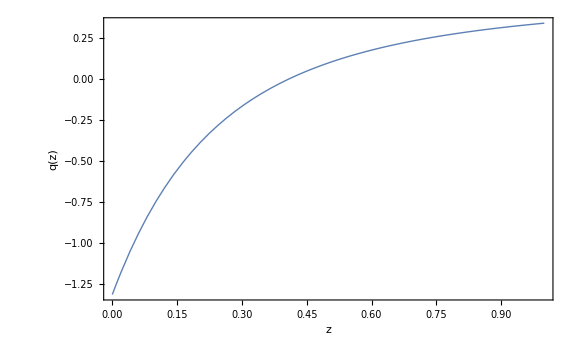

```mathematica
p02n=Plot[q[z],{z,0,1},PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma3[a_]=gamma059+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma3[a];
```

```mathematica
gamma059=0.59;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points3=Table[{z,omegade[z]},{z,0,1,0.01}]
points7=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.68},{0.01,0.675912},{0.02,0.671894},{0.03,0.667945},{0.04,0.664063},{0.05,0.660249},{0.06,0.656502},{0.07,0.652819},{0.08,0.649201},{0.09,0.645646},{0.1,0.642153},{0.11,0.638722},{0.12,0.635351},{0.13,0.632039},{0.14,0.628786},{0.15,0.62559},{0.16,0.62245},{0.17,0.619366},{0.18,0.616337},{0.19,0.61336},{0.2,0.610437},{0.21,0.607564},{0.22,0.604743},{0.23,0.601971},{0.24,0.599248},{0.25,0.596572},{0.26,0.593944},{0.27,0.591362},{0.28,0.588825},{0.29,0.586333},{0.3,0.583884},{0.31,0.581478},{0.32,0.579114},{0.33,0.576791},{0.34,0.574508},{0.35,0.572266},{0.36,0.570062},{0.37,0.567896},{0.38,0.565767},{0.39,0.563676},{0.4,0.56162},{0.41,0.5596},{0.42,0.557614},{0.43,0.555662},{0.44,0.553744},{0.45,0.551859},{0.46,0.550005},{0.47,0.548184},{0.48,0.546393},{0.49,0.544632},{0.5,0.542902},{0.51,0.5412},{0.52,0.539528},{0.53,0.537883},{0.54,0.536266},{0.55,0.534677},{0.56,0.533114},{0.57,0.531577},{0.58,0.530066},{0.59,0.52858},{0.6,0.527118},{0.61,0.525682},{0.62,0.524268},{0.63,0.522879},{0.64,0.521512},{0.65,0.520168},{0.66,0.518846},{0.67,0.517546},{0.68,0.516267},{0.69,0.51501},{0.7,0.513773},{0.71,0.512556},{0.72,0.511359},{0.73,0.510182},{0.74,0.509024},{0.75,0.507885},{0.76,0.506765},{0.77,0.505662},{0.78,0.504578},{0.79,0.503512},{0.8,0.502462},{0.81,0.50143},{0.82,0.500414},{0.83,0.499415},{0.84,0.498432},{0.85,0.497465},{0.86,0.496514},{0.87,0.495578},{0.88,0.494657},{0.89,0.493751},{0.9,0.49286},{0.91,0.491983},{0.92,0.49112},{0.93,0.490271},{0.94,0.489436},{0.95,0.488615},{0.96,0.487806},{0.97,0.487011},{0.98,0.486228},{0.99,0.485458},{1.,0.4847}}

{{0.,0.32},{0.01,0.324088},{0.02,0.328106},{0.03,0.332055},{0.04,0.335937},{0.05,0.339751},{0.06,0.343498},{0.07,0.347181},{0.08,0.350799},{0.09,0.354354},{0.1,0.357847},{0.11,0.361278},{0.12,0.364649},{0.13,0.367961},{0.14,0.371214},{0.15,0.37441},{0.16,0.37755},{0.17,0.380634},{0.18,0.383663},{0.19,0.38664},{0.2,0.389563},{0.21,0.392436},{0.22,0.395257},{0.23,0.398029},{0.24,0.400752},{0.25,0.403428},{0.26,0.406056},{0.27,0.408638},{0.28,0.411175},{0.29,0.413667},{0.3,0.416116},{0.31,0.418522},{0.32,0.420886},{0.33,0.423209},{0.34,0.425492},{0.35,0.427734},{0.36,0.429938},{0.37,0.432104},{0.38,0.434233},{0.39,0.436324},{0.4,0.43838},{0.41,0.4404},{0.42,0.442386},{0.43,0.444338},{0.44,0.446256},{0.45,0.448141},{0.46,0.449995},{0.47,0.451816},{0.48,0.453607},{0.49,0.455368},{0.5,0.457098},{0.51,0.4588},{0.52,0.460472},{0.53,0.462117},{0.54,0.463734},{0.55,0.465323},{0.56,0.466886},{0.57,0.468423},{0.58,0.469934},{0.59,0.47142},{0.6,0.472882},{0.61,0.474318},{0.62,0.475732},{0.63,0.477121},{0.64,0.478488},{0.65,0.479832},{0.66,0.481154},{0.67,0.482454},{0.68,0.483733},{0.69,0.48499},{0.7,0.486227},{0.71,0.487444},{0.72,0.488641},{0.73,0.489818},{0.74,0.490976},{0.75,0.492115},{0.76,0.493235},{0.77,0.494338},{0.78,0.495422},{0.79,0.496488},{0.8,0.497538},{0.81,0.49857},{0.82,0.499586},{0.83,0.500585},{0.84,0.501568},{0.85,0.502535},{0.86,0.503486},{0.87,0.504422},{0.88,0.505343},{0.89,0.506249},{0.9,0.50714},{0.91,0.508017},{0.92,0.50888},{0.93,0.509729},{0.94,0.510564},{0.95,0.511385},{0.96,0.512194},{0.97,0.512989},{0.98,0.513772},{0.99,0.514542},{1.,0.5153}}

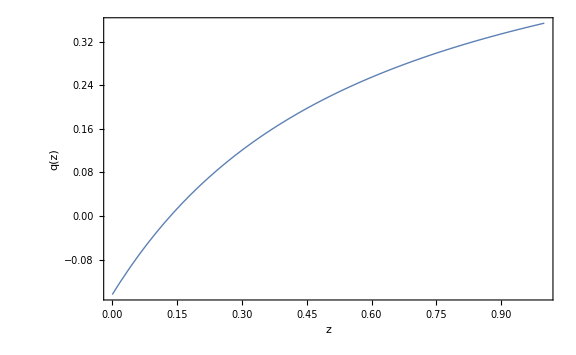

```mathematica
p02=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

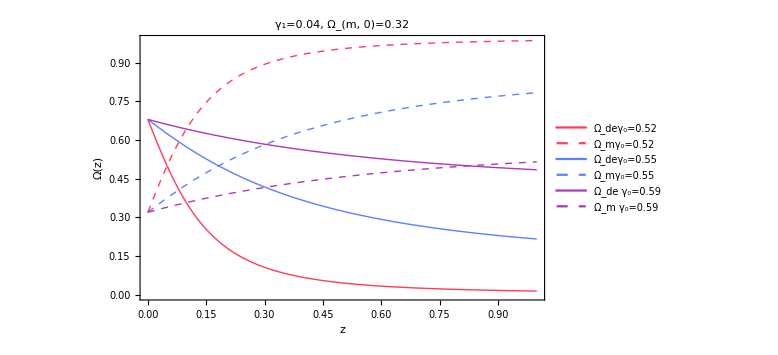

```mathematica
list2=ListLinePlot[{points1,points5,points2, points6, points3, points7}, PlotStyle->{{Thick, RGBColor[1,0.24,0.36]}, {Thick,Dashed, RGBColor[1,0.24,0.36]},{Thick, RGBColor[0.36,0.5,1]}, {Thick,Dashed, RGBColor[0.36,0.5,1]},{Thick, RGBColor[0.68,0.22,0.72]}, {Thick,Dashed, RGBColor[0.68,0.22,0.72]},{Thick, RGBColor[0.31,0.82,0]}, {Thick, Dashed,RGBColor[0.31,0.82,0]}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24,  FontFamily->"Helvetica"],Style["Ω(z)", Black, FontSize->24,  FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"Ω_deγ_0=0.52","Ω_mγ_0=0.52", "Ω_deγ_0=0.55","Ω_mγ_0=0.55", "Ω_de γ_0=0.59", "Ω_m γ_0=0.59","Ω_deγ_1=0.04", "Ω_mγ_1=0.04"}, Background->White, LabelStyle->{FontSize->7}, LegendMarkerSize->{{20,10}}],{Right, Center}], PlotLabel->Style["γ_1=0.04, Ω_(m, 0)=0.32", Black, FontSize->20,  FontFamily->"Helvetica"], Axes->False]
```

```mathematica
Export["omega(z)_gamma1_0.04_om0.32.pdf",list2,ImageResolution->500]
```

omega(z)_gamma1_0.04_om0.32.pdf